```mathematica
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m"
```

```mathematica
Omega
```

{{ω[1,1],ω[1,2],ω[1,3],ω[1,4],ω[1,5],ω[1,6],0},{ω[1,2],ω[2,2],ω[2,3],ω[2,4],ω[2,5],ω[2,6],0},{ω[1,3],ω[2,3],ω[3,3],ω[3,4],ω[3,5],ω[3,6],0},{ω[1,4],ω[2,4],ω[3,4],ω[4,4],ω[4,5],ω[4,6],0},{ω[1,5],ω[2,5],ω[3,5],ω[4,5],ω[5,5],ω[5,6],0},{ω[1,6],ω[2,6],ω[3,6],ω[4,6],ω[5,6],ω[6,6],0},{0,0,0,0,0,0,Δ}}

```mathematica
(*I2noise = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)]*)
(**)
(*I2 = Expand[(lf[1])*(lf[2])]*)
(*I2 = Expand[(lf[1]^2-1)*(lf[2]^2-1)]*)
I2 = Expand[(lf[1]^3-3*lf[1])*(lf[2]^3-3*lf[2])]
(*I2=Expand[(lf[1]^4-6*lf[1]^2+3)*(lf[2]^4-6*lf[2]^2+3)]*)
(**)
(*I3 = Expand[(1)*lf[2]*(lf[3])]*)
(*I3 = Expand[2*lf[1]*lf[2]*(lf[3]^2-1)]*)
I3 = Expand[(3*lf[1]^2-3)*lf[2]*(lf[3]^3-3*lf[3])]
(*I3 = Expand[(4*lf[1]^3-12*lf[1])*lf[2]*(lf[3]^4-6*lf[3]^2+3)]*)
(*I3 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*lf[2]*(lf[3]^5-10*lf[3]^3+15*lf[3])]*)
(*I3 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*lf[2]*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)]*)
(**)
(*I4 = Expand[(1)*(1)*(lf[3])*(lf[4])]*)
(*I4 = Expand[(2*lf[1])*(2*lf[2])*(lf[3]^2-1)*(lf[4]^2-1)]*)
I4 = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)*(lf[3]^3-3*lf[3])*(lf[4]^3-3*lf[4])]
(*I4 = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])*(lf[3]^4-6*lf[3]^2+3)*(lf[4]^4-6*lf[4]^2+3)]*)
(*I4 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*(5*lf[2]^4-30*lf[2]^2+15)*(lf[3]^5-10*lf[3]^3+15*lf[3])*(lf[4]^5-10*lf[4]^3+15*lf[4])]*)
(*I4 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*(6*lf[2]^5-60*lf[2]^3+90*lf[2])*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)*(lf[4]^6-15*lf[4]^4+45*lf[4]^2-15)]*)
```

9-18 λ[1]^2+3 λ[1]^4-18 λ[2]^2+36 λ[1]^2 λ[2]^2-6 λ[1]^4 λ[2]^2+3 λ[2]^4-6 λ[1]^2 λ[2]^4+λ[1]^4 λ[2]^4

-36 λ[1] λ[2]+12 λ[1]^3 λ[2]+72 λ[1] λ[2] λ[3]^2-24 λ[1]^3 λ[2] λ[3]^2-12 λ[1] λ[2] λ[3]^4+4 λ[1]^3 λ[2] λ[3]^4

1296 λ[1] λ[2]-432 λ[1]^3 λ[2]-432 λ[1] λ[2]^3+144 λ[1]^3 λ[2]^3-2592 λ[1] λ[2] λ[3]^2+864 λ[1]^3 λ[2] λ[3]^2+864 λ[1] λ[2]^3 λ[3]^2-288 λ[1]^3 λ[2]^3 λ[3]^2+432 λ[1] λ[2] λ[3]^4-144 λ[1]^3 λ[2] λ[3]^4-144 λ[1] λ[2]^3 λ[3]^4+48 λ[1]^3 λ[2]^3 λ[3]^4-2592 λ[1] λ[2] λ[4]^2+864 λ[1]^3 λ[2] λ[4]^2+864 λ[1] λ[2]^3 λ[4]^2-288 λ[1]^3 λ[2]^3 λ[4]^2+5184 λ[1] λ[2] λ[3]^2 λ[4]^2-1728 λ[1]^3 λ[2] λ[3]^2 λ[4]^2-1728 λ[1] λ[2]^3 λ[3]^2 λ[4]^2+576 λ[1]^3 λ[2]^3 λ[3]^2 λ[4]^2-864 λ[1] λ[2] λ[3]^4 λ[4]^2+288 λ[1]^3 λ[2] λ[3]^4 λ[4]^2+288 λ[1] λ[2]^3 λ[3]^4 λ[4]^2-96 λ[1]^3 λ[2]^3 λ[3]^4 λ[4]^2+432 λ[1] λ[2] λ[4]^4-144 λ[1]^3 λ[2] λ[4]^4-144 λ[1] λ[2]^3 λ[4]^4+48 λ[1]^3 λ[2]^3 λ[4]^4-864 λ[1] λ[2] λ[3]^2 λ[4]^4+288 λ[1]^3 λ[2] λ[3]^2 λ[4]^4+288 λ[1] λ[2]^3 λ[3]^2 λ[4]^4-96 λ[1]^3 λ[2]^3 λ[3]^2 λ[4]^4+144 λ[1] λ[2] λ[3]^4 λ[4]^4-48 λ[1]^3 λ[2] λ[3]^4 λ[4]^4-48 λ[1] λ[2]^3 λ[3]^4 λ[4]^4+16 λ[1]^3 λ[2]^3 λ[3]^4 λ[4]^4

```mathematica
IsserlisTheorem[I2]
```

9-18 ω[1,1]+9 ω[1,1]^2+72 ω[1,2]^2-72 ω[1,1] ω[1,2]^2+24 ω[1,2]^4-18 ω[2,2]+36 ω[1,1] ω[2,2]-18 ω[1,1]^2 ω[2,2]-72 ω[1,2]^2 ω[2,2]+72 ω[1,1] ω[1,2]^2 ω[2,2]+9 ω[2,2]^2-18 ω[1,1] ω[2,2]^2+9 ω[1,1]^2 ω[2,2]^2

```mathematica
a =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->m,ω[2,2]->ρ,ω[2,3]->ρ,ω[3,3]->ρ} ;
b= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->q,ω[2,2]->ρ,ω[2,3]->m,ω[3,3]->q} ;
c = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[1,4]->m,ω[2,2]->q,ω[2,3]->m,ω[2,4]->m,ω[3,3]->ρ,ω[3,4]->ρ,ω[4,4]->ρ} ;
d = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->q,ω[2,2]->q,ω[2,3]->q,ω[2,4]->q,ω[3,3]->q,ω[3,4]->q,ω[4,4]->q} ;
e = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->m,ω[2,2]->q,ω[2,3]->q,ω[2,4]->m,ω[3,3]->q,ω[3,4]->m,ω[4,4]->ρ} ;
f =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[2,2]->q,ω[2,3]->m,ω[3,3]->ρ} ;
g= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[2,2]->q,ω[2,3]->q,ω[3,3]->q} ;
h =IsserlisTheorem[I2] /.{ω[1,1]->1,ω[1,2]->1,ω[2,2]->1};
i = IsserlisTheorem[I2] /.{ω[1,1]->1,ω[1,2]->m,ω[2,2]->1};
mUpdate =FullSimplify[(a-b)]
qUpdate = FullSimplify[2*(f-g)+γ*(c+d-2*e)]
PopRisk = 2*h-2*i+Δ/2
```

12 m (q (-18+5 (9-7 q) q)-18 (-1+q) ρ+15 (-1+q) ρ^2+4 m^2 (-3+5 ρ))

24 (1920 m^6 γ (-3+7 ρ)+q (q (-18+5 q (9-7 q+18 (36+7 q (-36+q (117+11 q (-18+13 q)))) γ))+6 (1-q+12 q (-18+5 q (15+7 q (-4+3 q))) γ) ρ-3 (1-q+12 (-18+q (18+5 q (9+7 q (-4+3 q)))) γ) ρ^2-360 (3+q (-6+5 q)) γ ρ^3+210 (3+q (-6+5 q)) γ ρ^4)-8 m^4 (-1+36 γ (6-60 ρ+5 (q (9+14 q (-4+5 q))+30 q ρ+7 (2-5 q) ρ^2)))+12 m^2 (1+6720 q^3 γ (-1+ρ)-6300 q^4 γ (-1+ρ)+60 q^2 γ (45+ρ (-27+5 ρ (-9+7 ρ)))+ρ (-1+12 γ (18+5 ρ (-9+7 ρ)))-2 q (1-ρ+24 γ (9+ρ (9+5 ρ (-9+7 ρ))))))

48-48 m^4+Δ/2

```mathematica
mUpdateSpherical = Expand[FullSimplify[(mUpdate-m/2*qUpdate)/.{ρ->1,q->1}]]
```

96 m^3-96 m^5-246528 m γ-27648 m^3 γ+366336 m^5 γ-92160 m^7 γ

48.0005-48 x^4

-96 (-1/4+m^4/4)+96 (-1/6+m^6/6)

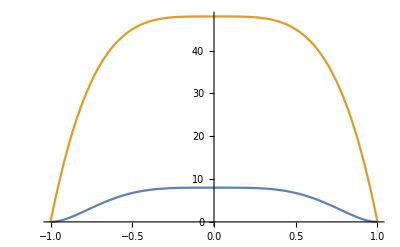

```mathematica
functionMUpdateSpherical[x_] = mUpdateSpherical /. {m->x, γ->0,Δ->.001};
functionPopRisk[x_] =PopRisk /.{m ->x,Δ->0.001}
EffectivePontentialSGD[m_]= -Integrate[functionMUpdateSpherical[x], {x,1,m}]
Plot[{EffectivePontentialSGD[m],functionPopRisk[m]},{m,-1,1}]
```

```mathematica
IsserlisTheorem[I4]
```

1296 ω[1,2]-1296 ω[1,1] ω[1,2]+864 ω[1,2]^3+5184 ω[1,2] ω[1,3]^2+5184 ω[1,2] ω[1,4]^2-1296 ω[1,2] ω[2,2]+1296 ω[1,1] ω[1,2] ω[2,2]-5184 ω[1,2] ω[1,3]^2 ω[2,2]-5184 ω[1,2] ω[1,4]^2 ω[2,2]-5184 ω[1,3] ω[2,3]+5184 ω[1,1] ω[1,3] ω[2,3]-10368 ω[1,2]^2 ω[1,3] ω[2,3]-3456 ω[1,3]^3 ω[2,3]-20736 ω[1,3] ω[1,4]^2 ω[2,3]+5184 ω[1,3] ω[2,2] ω[2,3]-5184 ω[1,1] ω[1,3] ω[2,2] ω[2,3]+3456 ω[1,3]^3 ω[2,2] ω[2,3]+20736 ω[1,3] ω[1,4]^2 ω[2,2] ω[2,3]+5184 ω[1,2] ω[2,3]^2-5184 ω[1,1] ω[1,2] ω[2,3]^2+10368 ω[1,2] ω[1,3]^2 ω[2,3]^2+20736 ω[1,2] ω[1,4]^2 ω[2,3]^2-3456 ω[1,3] ω[2,3]^3+3456 ω[1,1] ω[1,3] ω[2,3]^3-13824 ω[1,3] ω[1,4]^2 ω[2,3]^3-5184 ω[1,4] ω[2,4]+5184 ω[1,1] ω[1,4] ω[2,4]-10368 ω[1,2]^2 ω[1,4] ω[2,4]-20736 ω[1,3]^2 ω[1,4] ω[2,4]-3456 ω[1,4]^3 ω[2,4]+5184 ω[1,4] ω[2,2] ω[2,4]-5184 ω[1,1] ω[1,4] ω[2,2] ω[2,4]+20736 ω[1,3]^2 ω[1,4] ω[2,2] ω[2,4]+3456 ω[1,4]^3 ω[2,2] ω[2,4]+82944 ω[1,2] ω[1,3] ω[1,4] ω[2,3] ω[2,4]-20736 ω[1,4] ω[2,3]^2 ω[2,4]+20736 ω[1,1] ω[1,4] ω[2,3]^2 ω[2,4]-41472 ω[1,3]^2 ω[1,4] ω[2,3]^2 ω[2,4]-13824 ω[1,4]^3 ω[2,3]^2 ω[2,4]+5184 ω[1,2] ω[2,4]^2-5184 ω[1,1] ω[1,2] ω[2,4]^2+20736 ω[1,2] ω[1,3]^2 ω[2,4]^2+10368 ω[1,2] ω[1,4]^2 ω[2,4]^2-20736 ω[1,3] ω[2,3] ω[2,4]^2+20736 ω[1,1] ω[1,3] ω[2,3] ω[2,4]^2-13824 ω[1,3]^3 ω[2,3] ω[2,4]^2-41472 ω[1,3] ω[1,4]^2 ω[2,3] ω[2,4]^2-3456 ω[1,4] ω[2,4]^3+3456 ω[1,1] ω[1,4] ω[2,4]^3-13824 ω[1,3]^2 ω[1,4] ω[2,4]^3-2592 ω[1,2] ω[3,3]+2592 ω[1,1] ω[1,2] ω[3,3]-1728 ω[1,2]^3 ω[3,3]-5184 ω[1,2] ω[1,3]^2 ω[3,3]-10368 ω[1,2] ω[1,4]^2 ω[3,3]+2592 ω[1,2] ω[2,2] ω[3,3]-2592 ω[1,1] ω[1,2] ω[2,2] ω[3,3]+5184 ω[1,2] ω[1,3]^2 ω[2,2] ω[3,3]+10368 ω[1,2] ω[1,4]^2 ω[2,2] ω[3,3]+5184 ω[1,3] ω[2,3] ω[3,3]-5184 ω[1,1] ω[1,3] ω[2,3] ω[3,3]+10368 ω[1,2]^2 ω[1,3] ω[2,3] ω[3,3]+20736 ω[1,3] ω[1,4]^2 ω[2,3] ω[3,3]-5184 ω[1,3] ω[2,2] ω[2,3] ω[3,3]+5184 ω[1,1] ω[1,3] ω[2,2] ω[2,3] ω[3,3]-20736 ω[1,3] ω[1,4]^2 ω[2,2] ω[2,3] ω[3,3]-5184 ω[1,2] ω[2,3]^2 ω[3,3]+5184 ω[1,1] ω[1,2] ω[2,3]^2 ω[3,3]-20736 ω[1,2] ω[1,4]^2 ω[2,3]^2 ω[3,3]+10368 ω[1,4] ω[2,4] ω[3,3]-10368 ω[1,1] ω[1,4] ω[2,4] ω[3,3]+20736 ω[1,2]^2 ω[1,4] ω[2,4] ω[3,3]+20736 ω[1,3]^2 ω[1,4] ω[2,4] ω[3,3]+6912 ω[1,4]^3 ω[2,4] ω[3,3]-10368 ω[1,4] ω[2,2] ω[2,4] ω[3,3]+10368 ω[1,1] ω[1,4] ω[2,2] ω[2,4] ω[3,3]-20736 ω[1,3]^2 ω[1,4] ω[2,2] ω[2,4] ω[3,3]-6912 ω[1,4]^3 ω[2,2] ω[2,4] ω[3,3]-82944 ω[1,2] ω[1,3] ω[1,4] ω[2,3] ω[2,4] ω[3,3]+20736 ω[1,4] ω[2,3]^2 ω[2,4] ω[3,3]-20736 ω[1,1] ω[1,4] ω[2,3]^2 ω[2,4] ω[3,3]+13824 ω[1,4]^3 ω[2,3]^2 ω[2,4] ω[3,3]-10368 ω[1,2] ω[2,4]^2 ω[3,3]+10368 ω[1,1] ω[1,2] ω[2,4]^2 ω[3,3]-20736 ω[1,2] ω[1,3]^2 ω[2,4]^2 ω[3,3]-20736 ω[1,2] ω[1,4]^2 ω[2,4]^2 ω[3,3]+20736 ω[1,3] ω[2,3] ω[2,4]^2 ω[3,3]-20736 ω[1,1] ω[1,3] ω[2,3] ω[2,4]^2 ω[3,3]+41472 ω[1,3] ω[1,4]^2 ω[2,3] ω[2,4]^2 ω[3,3]+6912 ω[1,4] ω[2,4]^3 ω[3,3]-6912 ω[1,1] ω[1,4] ω[2,4]^3 ω[3,3]+13824 ω[1,3]^2 ω[1,4] ω[2,4]^3 ω[3,3]+1296 ω[1,2] ω[3,3]^2-1296 ω[1,1] ω[1,2] ω[3,3]^2+864 ω[1,2]^3 ω[3,3]^2+5184 ω[1,2] ω[1,4]^2 ω[3,3]^2-1296 ω[1,2] ω[2,2] ω[3,3]^2+1296 ω[1,1] ω[1,2] ω[2,2] ω[3,3]^2-5184 ω[1,2] ω[1,4]^2 ω[2,2] ω[3,3]^2-5184 ω[1,4] ω[2,4] ω[3,3]^2+5184 ω[1,1] ω[1,4] ω[2,4] ω[3,3]^2-10368 ω[1,2]^2 ω[1,4] ω[2,4] ω[3,3]^2-3456 ω[1,4]^3 ω[2,4] ω[3,3]^2+5184 ω[1,4] ω[2,2] ω[2,4] ω[3,3]^2-5184 ω[1,1] ω[1,4] ω[2,2] ω[2,4] ω[3,3]^2+3456 ω[1,4]^3 ω[2,2] ω[2,4] ω[3,3]^2+5184 ω[1,2] ω[2,4]^2 ω[3,3]^2-5184 ω[1,1] ω[1,2] ω[2,4]^2 ω[3,3]^2+10368 ω[1,2] ω[1,4]^2 ω[2,4]^2 ω[3,3]^2-3456 ω[1,4] ω[2,4]^3 ω[3,3]^2+3456 ω[1,1] ω[1,4] ω[2,4]^3 ω[3,3]^2-41472 ω[1,2] ω[1,3] ω[1,4] ω[3,4]+41472 ω[1,2] ω[1,3] ω[1,4] ω[2,2] ω[3,4]+20736 ω[1,4] ω[2,3] ω[3,4]-20736 ω[1,1] ω[1,4] ω[2,3] ω[3,4]+41472 ω[1,2]^2 ω[1,4] ω[2,3] ω[3,4]+41472 ω[1,3]^2 ω[1,4] ω[2,3] ω[3,4]+13824 ω[1,4]^3 ω[2,3] ω[3,4]-20736 ω[1,4] ω[2,2] ω[2,3] ω[3,4]+20736 ω[1,1] ω[1,4] ω[2,2] ω[2,3] ω[3,4]-41472 ω[1,3]^2 ω[1,4] ω[2,2] ω[2,3] ω[3,4]-13824 ω[1,4]^3 ω[2,2] ω[2,3] ω[3,4]-82944 ω[1,2] ω[1,3] ω[1,4] ω[2,3]^2 ω[3,4]+13824 ω[1,4] ω[2,3]^3 ω[3,4]-13824 ω[1,1] ω[1,4] ω[2,3]^3 ω[3,4]+9216 ω[1,4]^3 ω[2,3]^3 ω[3,4]+20736 ω[1,3] ω[2,4] ω[3,4]-20736 ω[1,1] ω[1,3] ω[2,4] ω[3,4]+41472 ω[1,2]^2 ω[1,3] ω[2,4] ω[3,4]+13824 ω[1,3]^3 ω[2,4] ω[3,4]+41472 ω[1,3] ω[1,4]^2 ω[2,4] ω[3,4]-20736 ω[1,3] ω[2,2] ω[2,4] ω[3,4]+20736 ω[1,1] ω[1,3] ω[2,2] ω[2,4] ω[3,4]-13824 ω[1,3]^3 ω[2,2] ω[2,4] ω[3,4]-41472 ω[1,3] ω[1,4]^2 ω[2,2] ω[2,4] ω[3,4]-41472 ω[1,2] ω[2,3] ω[2,4] ω[3,4]+41472 ω[1,1] ω[1,2] ω[2,3] ω[2,4] ω[3,4]-82944 ω[1,2] ω[1,3]^2 ω[2,3] ω[2,4] ω[3,4]-82944 ω[1,2] ω[1,4]^2 ω[2,3] ω[2,4] ω[3,4]+41472 ω[1,3] ω[2,3]^2 ω[2,4] ω[3,4]-41472 ω[1,1] ω[1,3] ω[2,3]^2 ω[2,4] ω[3,4]+82944 ω[1,3] ω[1,4]^2 ω[2,3]^2 ω[2,4] ω[3,4]-82944 ω[1,2] ω[1,3] ω[1,4] ω[2,4]^2 ω[3,4]+41472 ω[1,4] ω[2,3] ω[2,4]^2 ω[3,4]-41472 ω[1,1] ω[1,4] ω[2,3] ω[2,4]^2 ω[3,4]+82944 ω[1,3]^2 ω[1,4] ω[2,3] ω[2,4]^2 ω[3,4]+13824 ω[1,3] ω[2,4]^3 ω[3,4]-13824 ω[1,1] ω[1,3] ω[2,4]^3 ω[3,4]+9216 ω[1,3]^3 ω[2,4]^3 ω[3,4]+41472 ω[1,2] ω[1,3] ω[1,4] ω[3,3] ω[3,4]-41472 ω[1,2] ω[1,3] ω[1,4] ω[2,2] ω[3,3] ω[3,4]-20736 ω[1,4] ω[2,3] ω[3,3] ω[3,4]+20736 ω[1,1] ω[1,4] ω[2,3] ω[3,3] ω[3,4]-41472 ω[1,2]^2 ω[1,4] ω[2,3] ω[3,3] ω[3,4]-13824 ω[1,4]^3 ω[2,3] ω[3,3] ω[3,4]+20736 ω[1,4] ω[2,2] ω[2,3] ω[3,3] ω[3,4]-20736 ω[1,1] ω[1,4] ω[2,2] ω[2,3] ω[3,3] ω[3,4]+13824 ω[1,4]^3 ω[2,2] ω[2,3] ω[3,3] ω[3,4]-20736 ω[1,3] ω[2,4] ω[3,3] ω[3,4]+20736 ω[1,1] ω[1,3] ω[2,4] ω[3,3] ω[3,4]-41472 ω[1,2]^2 ω[1,3] ω[2,4] ω[3,3] ω[3,4]-41472 ω[1,3] ω[1,4]^2 ω[2,4] ω[3,3] ω[3,4]+20736 ω[1,3] ω[2,2] ω[2,4] ω[3,3] ω[3,4]-20736 ω[1,1] ω[1,3] ω[2,2] ω[2,4] ω[3,3] ω[3,4]+41472 ω[1,3] ω[1,4]^2 ω[2,2] ω[2,4] ω[3,3] ω[3,4]+41472 ω[1,2] ω[2,3] ω[2,4] ω[3,3] ω[3,4]-41472 ω[1,1] ω[1,2] ω[2,3] ω[2,4] ω[3,3] ω[3,4]+82944 ω[1,2] ω[1,4]^2 ω[2,3] ω[2,4] ω[3,3] ω[3,4]+82944 ω[1,2] ω[1,3] ω[1,4] ω[2,4]^2 ω[3,3] ω[3,4]-41472 ω[1,4] ω[2,3] ω[2,4]^2 ω[3,3] ω[3,4]+41472 ω[1,1] ω[1,4] ω[2,3] ω[2,4]^2 ω[3,3] ω[3,4]-13824 ω[1,3] ω[2,4]^3 ω[3,3] ω[3,4]+13824 ω[1,1] ω[1,3] ω[2,4]^3 ω[3,3] ω[3,4]+10368 ω[1,2] ω[3,4]^2-10368 ω[1,1] ω[1,2] ω[3,4]^2+6912 ω[1,2]^3 ω[3,4]^2+20736 ω[1,2] ω[1,3]^2 ω[3,4]^2+20736 ω[1,2] ω[1,4]^2 ω[3,4]^2-10368 ω[1,2] ω[2,2] ω[3,4]^2+10368 ω[1,1] ω[1,2] ω[2,2] ω[3,4]^2-20736 ω[1,2] ω[1,3]^2 ω[2,2] ω[3,4]^2-20736 ω[1,2] ω[1,4]^2 ω[2,2] ω[3,4]^2-20736 ω[1,3] ω[2,3] ω[3,4]^2+20736 ω[1,1] ω[1,3] ω[2,3] ω[3,4]^2-41472 ω[1,2]^2 ω[1,3] ω[2,3] ω[3,4]^2-41472 ω[1,3] ω[1,4]^2 ω[2,3] ω[3,4]^2+20736 ω[1,3] ω[2,2] ω[2,3] ω[3,4]^2-20736 ω[1,1] ω[1,3] ω[2,2] ω[2,3] ω[3,4]^2+41472 ω[1,3] ω[1,4]^2 ω[2,2] ω[2,3] ω[3,4]^2+20736 ω[1,2] ω[2,3]^2 ω[3,4]^2-20736 ω[1,1] ω[1,2] ω[2,3]^2 ω[3,4]^2+41472 ω[1,2] ω[1,4]^2 ω[2,3]^2 ω[3,4]^2-20736 ω[1,4] ω[2,4] ω[3,4]^2+20736 ω[1,1] ω[1,4] ω[2,4] ω[3,4]^2-41472 ω[1,2]^2 ω[1,4] ω[2,4] ω[3,4]^2-41472 ω[1,3]^2 ω[1,4] ω[2,4] ω[3,4]^2+20736 ω[1,4] ω[2,2] ω[2,4] ω[3,4]^2-20736 ω[1,1] ω[1,4] ω[2,2] ω[2,4] ω[3,4]^2+41472 ω[1,3]^2 ω[1,4] ω[2,2] ω[2,4] ω[3,4]^2+165888 ω[1,2] ω[1,3] ω[1,4] ω[2,3] ω[2,4] ω[3,4]^2-41472 ω[1,4] ω[2,3]^2 ω[2,4] ω[3,4]^2+41472 ω[1,1] ω[1,4] ω[2,3]^2 ω[2,4] ω[3,4]^2+20736 ω[1,2] ω[2,4]^2 ω[3,4]^2-20736 ω[1,1] ω[1,2] ω[2,4]^2 ω[3,4]^2+41472 ω[1,2] ω[1,3]^2 ω[2,4]^2 ω[3,4]^2-41472 ω[1,3] ω[2,3] ω[2,4]^2 ω[3,4]^2+41472 ω[1,1] ω[1,3] ω[2,3] ω[2,4]^2 ω[3,4]^2-10368 ω[1,2] ω[3,3] ω[3,4]^2+10368 ω[1,1] ω[1,2] ω[3,3] ω[3,4]^2-6912 ω[1,2]^3 ω[3,3] ω[3,4]^2-20736 ω[1,2] ω[1,4]^2 ω[3,3] ω[3,4]^2+10368 ω[1,2] ω[2,2] ω[3,3] ω[3,4]^2-10368 ω[1,1] ω[1,2] ω[2,2] ω[3,3] ω[3,4]^2+20736 ω[1,2] ω[1,4]^2 ω[2,2] ω[3,3] ω[3,4]^2+20736 ω[1,4] ω[2,4] ω[3,3] ω[3,4]^2-20736 ω[1,1] ω[1,4] ω[2,4] ω[3,3] ω[3,4]^2+41472 ω[1,2]^2 ω[1,4] ω[2,4] ω[3,3] ω[3,4]^2-20736 ω[1,4] ω[2,2] ω[2,4] ω[3,3] ω[3,4]^2+20736 ω[1,1] ω[1,4] ω[2,2] ω[2,4] ω[3,3] ω[3,4]^2-20736 ω[1,2] ω[2,4]^2 ω[3,3] ω[3,4]^2+20736 ω[1,1] ω[1,2] ω[2,4]^2 ω[3,3] ω[3,4]^2-27648 ω[1,2] ω[1,3] ω[1,4] ω[3,4]^3+27648 ω[1,2] ω[1,3] ω[1,4] ω[2,2] ω[3,4]^3+13824 ω[1,4] ω[2,3] ω[3,4]^3-13824 ω[1,1] ω[1,4] ω[2,3] ω[3,4]^3+27648 ω[1,2]^2 ω[1,4] ω[2,3] ω[3,4]^3-13824 ω[1,4] ω[2,2] ω[2,3] ω[3,4]^3+13824 ω[1,1] ω[1,4] ω[2,2] ω[2,3] ω[3,4]^3+13824 ω[1,3] ω[2,4] ω[3,4]^3-13824 ω[1,1] ω[1,3] ω[2,4] ω[3,4]^3+27648 ω[1,2]^2 ω[1,3] ω[2,4] ω[3,4]^3-13824 ω[1,3] ω[2,2] ω[2,4] ω[3,4]^3+13824 ω[1,1] ω[1,3] ω[2,2] ω[2,4] ω[3,4]^3-27648 ω[1,2] ω[2,3] ω[2,4] ω[3,4]^3+27648 ω[1,1] ω[1,2] ω[2,3] ω[2,4] ω[3,4]^3+3456 ω[1,2] ω[3,4]^4-3456 ω[1,1] ω[1,2] ω[3,4]^4+2304 ω[1,2]^3 ω[3,4]^4-3456 ω[1,2] ω[2,2] ω[3,4]^4+3456 ω[1,1] ω[1,2] ω[2,2] ω[3,4]^4-2592 ω[1,2] ω[4,4]+2592 ω[1,1] ω[1,2] ω[4,4]-1728 ω[1,2]^3 ω[4,4]-10368 ω[1,2] ω[1,3]^2 ω[4,4]-5184 ω[1,2] ω[1,4]^2 ω[4,4]+2592 ω[1,2] ω[2,2] ω[4,4]-2592 ω[1,1] ω[1,2] ω[2,2] ω[4,4]+10368 ω[1,2] ω[1,3]^2 ω[2,2] ω[4,4]+5184 ω[1,2] ω[1,4]^2 ω[2,2] ω[4,4]+10368 ω[1,3] ω[2,3] ω[4,4]-10368 ω[1,1] ω[1,3] ω[2,3] ω[4,4]+20736 ω[1,2]^2 ω[1,3] ω[2,3] ω[4,4]+6912 ω[1,3]^3 ω[2,3] ω[4,4]+20736 ω[1,3] ω[1,4]^2 ω[2,3] ω[4,4]-10368 ω[1,3] ω[2,2] ω[2,3] ω[4,4]+10368 ω[1,1] ω[1,3] ω[2,2] ω[2,3] ω[4,4]-6912 ω[1,3]^3 ω[2,2] ω[2,3] ω[4,4]-20736 ω[1,3] ω[1,4]^2 ω[2,2] ω[2,3] ω[4,4]-10368 ω[1,2] ω[2,3]^2 ω[4,4]+10368 ω[1,1] ω[1,2] ω[2,3]^2 ω[4,4]-20736 ω[1,2] ω[1,3]^2 ω[2,3]^2 ω[4,4]-20736 ω[1,2] ω[1,4]^2 ω[2,3]^2 ω[4,4]+6912 ω[1,3] ω[2,3]^3 ω[4,4]-6912 ω[1,1] ω[1,3] ω[2,3]^3 ω[4,4]+13824 ω[1,3] ω[1,4]^2 ω[2,3]^3 ω[4,4]+5184 ω[1,4] ω[2,4] ω[4,4]-5184 ω[1,1] ω[1,4] ω[2,4] ω[4,4]+10368 ω[1,2]^2 ω[1,4] ω[2,4] ω[4,4]+20736 ω[1,3]^2 ω[1,4] ω[2,4] ω[4,4]-5184 ω[1,4] ω[2,2] ω[2,4] ω[4,4]+5184 ω[1,1] ω[1,4] ω[2,2] ω[2,4] ω[4,4]-20736 ω[1,3]^2 ω[1,4] ω[2,2] ω[2,4] ω[4,4]-82944 ω[1,2] ω[1,3] ω[1,4] ω[2,3] ω[2,4] ω[4,4]+20736 ω[1,4] ω[2,3]^2 ω[2,4] ω[4,4]-20736 ω[1,1] ω[1,4] ω[2,3]^2 ω[2,4] ω[4,4]+41472 ω[1,3]^2 ω[1,4] ω[2,3]^2 ω[2,4] ω[4,4]-5184 ω[1,2] ω[2,4]^2 ω[4,4]+5184 ω[1,1] ω[1,2] ω[2,4]^2 ω[4,4]-20736 ω[1,2] ω[1,3]^2 ω[2,4]^2 ω[4,4]+20736 ω[1,3] ω[2,3] ω[2,4]^2 ω[4,4]-20736 ω[1,1] ω[1,3] ω[2,3] ω[2,4]^2 ω[4,4]+13824 ω[1,3]^3 ω[2,3] ω[2,4]^2 ω[4,4]+5184 ω[1,2] ω[3,3] ω[4,4]-5184 ω[1,1] ω[1,2] ω[3,3] ω[4,4]+3456 ω[1,2]^3 ω[3,3] ω[4,4]+10368 ω[1,2] ω[1,3]^2 ω[3,3] ω[4,4]+10368 ω[1,2] ω[1,4]^2 ω[3,3] ω[4,4]-5184 ω[1,2] ω[2,2] ω[3,3] ω[4,4]+5184 ω[1,1] ω[1,2] ω[2,2] ω[3,3] ω[4,4]-10368 ω[1,2] ω[1,3]^2 ω[2,2] ω[3,3] ω[4,4]-10368 ω[1,2] ω[1,4]^2 ω[2,2] ω[3,3] ω[4,4]-10368 ω[1,3] ω[2,3] ω[3,3] ω[4,4]+10368 ω[1,1] ω[1,3] ω[2,3] ω[3,3] ω[4,4]-20736 ω[1,2]^2 ω[1,3] ω[2,3] ω[3,3] ω[4,4]-20736 ω[1,3] ω[1,4]^2 ω[2,3] ω[3,3] ω[4,4]+10368 ω[1,3] ω[2,2] ω[2,3] ω[3,3] ω[4,4]-10368 ω[1,1] ω[1,3] ω[2,2] ω[2,3] ω[3,3] ω[4,4]+20736 ω[1,3] ω[1,4]^2 ω[2,2] ω[2,3] ω[3,3] ω[4,4]+10368 ω[1,2] ω[2,3]^2 ω[3,3] ω[4,4]-10368 ω[1,1] ω[1,2] ω[2,3]^2 ω[3,3] ω[4,4]+20736 ω[1,2] ω[1,4]^2 ω[2,3]^2 ω[3,3] ω[4,4]-10368 ω[1,4] ω[2,4] ω[3,3] ω[4,4]+10368 ω[1,1] ω[1,4] ω[2,4] ω[3,3] ω[4,4]-20736 ω[1,2]^2 ω[1,4] ω[2,4] ω[3,3] ω[4,4]-20736 ω[1,3]^2 ω[1,4] ω[2,4] ω[3,3] ω[4,4]+10368 ω[1,4] ω[2,2] ω[2,4] ω[3,3] ω[4,4]-10368 ω[1,1] ω[1,4] ω[2,2] ω[2,4] ω[3,3] ω[4,4]+20736 ω[1,3]^2 ω[1,4] ω[2,2] ω[2,4] ω[3,3] ω[4,4]+82944 ω[1,2] ω[1,3] ω[1,4] ω[2,3] ω[2,4] ω[3,3] ω[4,4]-20736 ω[1,4] ω[2,3]^2 ω[2,4] ω[3,3] ω[4,4]+20736 ω[1,1] ω[1,4] ω[2,3]^2 ω[2,4] ω[3,3] ω[4,4]+10368 ω[1,2] ω[2,4]^2 ω[3,3] ω[4,4]-10368 ω[1,1] ω[1,2] ω[2,4]^2 ω[3,3] ω[4,4]+20736 ω[1,2] ω[1,3]^2 ω[2,4]^2 ω[3,3] ω[4,4]-20736 ω[1,3] ω[2,3] ω[2,4]^2 ω[3,3] ω[4,4]+20736 ω[1,1] ω[1,3] ω[2,3] ω[2,4]^2 ω[3,3] ω[4,4]-2592 ω[1,2] ω[3,3]^2 ω[4,4]+2592 ω[1,1] ω[1,2] ω[3,3]^2 ω[4,4]-1728 ω[1,2]^3 ω[3,3]^2 ω[4,4]-5184 ω[1,2] ω[1,4]^2 ω[3,3]^2 ω[4,4]+2592 ω[1,2] ω[2,2] ω[3,3]^2 ω[4,4]-2592 ω[1,1] ω[1,2] ω[2,2] ω[3,3]^2 ω[4,4]+5184 ω[1,2] ω[1,4]^2 ω[2,2] ω[3,3]^2 ω[4,4]+5184 ω[1,4] ω[2,4] ω[3,3]^2 ω[4,4]-5184 ω[1,1] ω[1,4] ω[2,4] ω[3,3]^2 ω[4,4]+10368 ω[1,2]^2 ω[1,4] ω[2,4] ω[3,3]^2 ω[4,4]-5184 ω[1,4] ω[2,2] ω[2,4] ω[3,3]^2 ω[4,4]+5184 ω[1,1] ω[1,4] ω[2,2] ω[2,4] ω[3,3]^2 ω[4,4]-5184 ω[1,2] ω[2,4]^2 ω[3,3]^2 ω[4,4]+5184 ω[1,1] ω[1,2] ω[2,4]^2 ω[3,3]^2 ω[4,4]+41472 ω[1,2] ω[1,3] ω[1,4] ω[3,4] ω[4,4]-41472 ω[1,2] ω[1,3] ω[1,4] ω[2,2] ω[3,4] ω[4,4]-20736 ω[1,4] ω[2,3] ω[3,4] ω[4,4]+20736 ω[1,1] ω[1,4] ω[2,3] ω[3,4] ω[4,4]-41472 ω[1,2]^2 ω[1,4] ω[2,3] ω[3,4] ω[4,4]-41472 ω[1,3]^2 ω[1,4] ω[2,3] ω[3,4] ω[4,4]+20736 ω[1,4] ω[2,2] ω[2,3] ω[3,4] ω[4,4]-20736 ω[1,1] ω[1,4] ω[2,2] ω[2,3] ω[3,4] ω[4,4]+41472 ω[1,3]^2 ω[1,4] ω[2,2] ω[2,3] ω[3,4] ω[4,4]+82944 ω[1,2] ω[1,3] ω[1,4] ω[2,3]^2 ω[3,4] ω[4,4]-13824 ω[1,4] ω[2,3]^3 ω[3,4] ω[4,4]+13824 ω[1,1] ω[1,4] ω[2,3]^3 ω[3,4] ω[4,4]-20736 ω[1,3] ω[2,4] ω[3,4] ω[4,4]+20736 ω[1,1] ω[1,3] ω[2,4] ω[3,4] ω[4,4]-41472 ω[1,2]^2 ω[1,3] ω[2,4] ω[3,4] ω[4,4]-13824 ω[1,3]^3 ω[2,4] ω[3,4] ω[4,4]+20736 ω[1,3] ω[2,2] ω[2,4] ω[3,4] ω[4,4]-20736 ω[1,1] ω[1,3] ω[2,2] ω[2,4] ω[3,4] ω[4,4]+13824 ω[1,3]^3 ω[2,2] ω[2,4] ω[3,4] ω[4,4]+41472 ω[1,2] ω[2,3] ω[2,4] ω[3,4] ω[4,4]-41472 ω[1,1] ω[1,2] ω[2,3] ω[2,4] ω[3,4] ω[4,4]+82944 ω[1,2] ω[1,3]^2 ω[2,3] ω[2,4] ω[3,4] ω[4,4]-41472 ω[1,3] ω[2,3]^2 ω[2,4] ω[3,4] ω[4,4]+41472 ω[1,1] ω[1,3] ω[2,3]^2 ω[2,4] ω[3,4] ω[4,4]-41472 ω[1,2] ω[1,3] ω[1,4] ω[3,3] ω[3,4] ω[4,4]+41472 ω[1,2] ω[1,3] ω[1,4] ω[2,2] ω[3,3] ω[3,4] ω[4,4]+20736 ω[1,4] ω[2,3] ω[3,3] ω[3,4] ω[4,4]-20736 ω[1,1] ω[1,4] ω[2,3] ω[3,3] ω[3,4] ω[4,4]+41472 ω[1,2]^2 ω[1,4] ω[2,3] ω[3,3] ω[3,4] ω[4,4]-20736 ω[1,4] ω[2,2] ω[2,3] ω[3,3] ω[3,4] ω[4,4]+20736 ω[1,1] ω[1,4] ω[2,2] ω[2,3] ω[3,3] ω[3,4] ω[4,4]+20736 ω[1,3] ω[2,4] ω[3,3] ω[3,4] ω[4,4]-20736 ω[1,1] ω[1,3] ω[2,4] ω[3,3] ω[3,4] ω[4,4]+41472 ω[1,2]^2 ω[1,3] ω[2,4] ω[3,3] ω[3,4] ω[4,4]-20736 ω[1,3] ω[2,2] ω[2,4] ω[3,3] ω[3,4] ω[4,4]+20736 ω[1,1] ω[1,3] ω[2,2] ω[2,4] ω[3,3] ω[3,4] ω[4,4]-41472 ω[1,2] ω[2,3] ω[2,4] ω[3,3] ω[3,4] ω[4,4]+41472 ω[1,1] ω[1,2] ω[2,3] ω[2,4] ω[3,3] ω[3,4] ω[4,4]-10368 ω[1,2] ω[3,4]^2 ω[4,4]+10368 ω[1,1] ω[1,2] ω[3,4]^2 ω[4,4]-6912 ω[1,2]^3 ω[3,4]^2 ω[4,4]-20736 ω[1,2] ω[1,3]^2 ω[3,4]^2 ω[4,4]+10368 ω[1,2] ω[2,2] ω[3,4]^2 ω[4,4]-10368 ω[1,1] ω[1,2] ω[2,2] ω[3,4]^2 ω[4,4]+20736 ω[1,2] ω[1,3]^2 ω[2,2] ω[3,4]^2 ω[4,4]+20736 ω[1,3] ω[2,3] ω[3,4]^2 ω[4,4]-20736 ω[1,1] ω[1,3] ω[2,3] ω[3,4]^2 ω[4,4]+41472 ω[1,2]^2 ω[1,3] ω[2,3] ω[3,4]^2 ω[4,4]-20736 ω[1,3] ω[2,2] ω[2,3] ω[3,4]^2 ω[4,4]+20736 ω[1,1] ω[1,3] ω[2,2] ω[2,3] ω[3,4]^2 ω[4,4]-20736 ω[1,2] ω[2,3]^2 ω[3,4]^2 ω[4,4]+20736 ω[1,1] ω[1,2] ω[2,3]^2 ω[3,4]^2 ω[4,4]+10368 ω[1,2] ω[3,3] ω[3,4]^2 ω[4,4]-10368 ω[1,1] ω[1,2] ω[3,3] ω[3,4]^2 ω[4,4]+6912 ω[1,2]^3 ω[3,3] ω[3,4]^2 ω[4,4]-10368 ω[1,2] ω[2,2] ω[3,3] ω[3,4]^2 ω[4,4]+10368 ω[1,1] ω[1,2] ω[2,2] ω[3,3] ω[3,4]^2 ω[4,4]+1296 ω[1,2] ω[4,4]^2-1296 ω[1,1] ω[1,2] ω[4,4]^2+864 ω[1,2]^3 ω[4,4]^2+5184 ω[1,2] ω[1,3]^2 ω[4,4]^2-1296 ω[1,2] ω[2,2] ω[4,4]^2+1296 ω[1,1] ω[1,2] ω[2,2] ω[4,4]^2-5184 ω[1,2] ω[1,3]^2 ω[2,2] ω[4,4]^2-5184 ω[1,3] ω[2,3] ω[4,4]^2+5184 ω[1,1] ω[1,3] ω[2,3] ω[4,4]^2-10368 ω[1,2]^2 ω[1,3] ω[2,3] ω[4,4]^2-3456 ω[1,3]^3 ω[2,3] ω[4,4]^2+5184 ω[1,3] ω[2,2] ω[2,3] ω[4,4]^2-5184 ω[1,1] ω[1,3] ω[2,2] ω[2,3] ω[4,4]^2+3456 ω[1,3]^3 ω[2,2] ω[2,3] ω[4,4]^2+5184 ω[1,2] ω[2,3]^2 ω[4,4]^2-5184 ω[1,1] ω[1,2] ω[2,3]^2 ω[4,4]^2+10368 ω[1,2] ω[1,3]^2 ω[2,3]^2 ω[4,4]^2-3456 ω[1,3] ω[2,3]^3 ω[4,4]^2+3456 ω[1,1] ω[1,3] ω[2,3]^3 ω[4,4]^2-2592 ω[1,2] ω[3,3] ω[4,4]^2+2592 ω[1,1] ω[1,2] ω[3,3] ω[4,4]^2-1728 ω[1,2]^3 ω[3,3] ω[4,4]^2-5184 ω[1,2] ω[1,3]^2 ω[3,3] ω[4,4]^2+2592 ω[1,2] ω[2,2] ω[3,3] ω[4,4]^2-2592 ω[1,1] ω[1,2] ω[2,2] ω[3,3] ω[4,4]^2+5184 ω[1,2] ω[1,3]^2 ω[2,2] ω[3,3] ω[4,4]^2+5184 ω[1,3] ω[2,3] ω[3,3] ω[4,4]^2-5184 ω[1,1] ω[1,3] ω[2,3] ω[3,3] ω[4,4]^2+10368 ω[1,2]^2 ω[1,3] ω[2,3] ω[3,3] ω[4,4]^2-5184 ω[1,3] ω[2,2] ω[2,3] ω[3,3] ω[4,4]^2+5184 ω[1,1] ω[1,3] ω[2,2] ω[2,3] ω[3,3] ω[4,4]^2-5184 ω[1,2] ω[2,3]^2 ω[3,3] ω[4,4]^2+5184 ω[1,1] ω[1,2] ω[2,3]^2 ω[3,3] ω[4,4]^2+1296 ω[1,2] ω[3,3]^2 ω[4,4]^2-1296 ω[1,1] ω[1,2] ω[3,3]^2 ω[4,4]^2+864 ω[1,2]^3 ω[3,3]^2 ω[4,4]^2-1296 ω[1,2] ω[2,2] ω[3,3]^2 ω[4,4]^2+1296 ω[1,1] ω[1,2] ω[2,2] ω[3,3]^2 ω[4,4]^2

```mathematica
FortranForm[IsserlisTheorem[I2noise]/.{ω->c}]
```

I2noise

```mathematica
FortranForm[IsserlisTheorem[I2]/.{ω->c}]
```

9 - 18*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1) + 
     -  9*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)**2 + 
     -  72*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2 - 
     -  72*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2 + 
     -  24*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**4 - 
     -  18*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) + 
     -  36*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) - 
     -  18*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) - 
     -  72*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) + 
     -  72*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) + 
     -  9*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)**2 - 
     -  18*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)**2 + 
     -  9*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)**2

```mathematica
FortranForm[IsserlisTheorem[I3]/.{ω->c}]
```

-36*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2) + 
     -  36*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2) - 
     -  144*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2 + 
     -  144*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) - 
     -  144*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) + 
     -  96*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) + 
     -  72*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  72*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  144*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  144*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  144*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  36*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3)**2 + 
     -  36*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3)**2

```mathematica
FortranForm[IsserlisTheorem[I4]/.{ω->c}]
```

1296*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2) - 
     -  1296*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2) + 
     -  864*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**3 + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2 + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2 - 
     -  1296*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) + 
     -  1296*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) - 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) - 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) + 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2 - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2 + 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2 + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2 - 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**3 + 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**3 - 
     -  13824*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**3 - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) - 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) - 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) + 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) + 
     -  82944*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) - 
     -  41472*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) - 
     -  13824*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 + 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 - 
     -  13824*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 - 
     -  41472*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2 - 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**3 + 
     -  3456*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**3 - 
     -  13824*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**3 - 
     -  2592*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  2592*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  1728*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  2592*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  2592*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  5184*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  6912*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  6912*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  82944*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  13824*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  10368*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  20736*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  41472*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,3)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  6912*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) - 
     -  6912*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,1)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  13824*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,3)**2*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,4)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(2,4)**3*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(3,3) + 
     -  1296*(-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -      322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 18144*q*ρ**2 + 
     -      622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 483840*m**2*q*ρ**3 + 
     -      51840*q**2*ρ**3 + 604800*m**2*q**2*ρ**3 - 43200*q**3*ρ**3 + 15120*q*ρ**4 - 30240*q**2*ρ**4 + 25200*q**3*ρ**4)(1,2)*
     -   (-10368*m**2 - 96768*m**4 - 138240*m**6 + 1296*q + 41472*m**2*q + 241920*m**4*q - 2592*q**2 - 51840*m**2*q**2 + 2160*q**3 + 72576*m**2*ρ + 414720*m**4*ρ + 
     -       322560*m**6*ρ - 5184*q*ρ - 290304*m**2*q*ρ - 1036800*m**4*q*ρ + 10368*q**2*ρ + 362880*m**2*q**2*ρ - 8640*q**3*ρ - 155520*m**2*ρ**2 - 483840*m**4*ρ**2 + 
     -       18144*q*ρ**2 + 622080*m**2*q*ρ**2 + 1209600*m**4*q*ρ**2 - 36288*q**2*ρ**2 - 777600*m**2*q**2*ρ**2 + 30240*q**3*ρ**2 + 120960*m**2*ρ**3 - 25920*q*ρ**3 - 
     -       483840*m**2*q*ρ**3 + 51840*q**2*ρ**3 + 604800*m**2*q*